# :d83d:dce1 Bset 3: The power of LTI

```mathematica
SetDirectory@NotebookDirectory[];
<<"../MMA library.m"
```

## Guitar Stairwell

```mathematica
With[{context="p4`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{data=Import["provided files/guitar_stairwell.mat","LabeledData"]},
fs=("Fs"/.data)[[1,1]];
hstairwell=("h_stairwell"/.data)[[All,1]];
x=("x"/.data)[[All,1]];
]
```

```mathematica
playSound[x,fs]
```

```mathematica
playSound[hstairwell,fs]
```

```mathematica
mutated=ListConvolve[hstairwell,x,{1,-1},0];
mutated/=Max@Abs@mutated;
```

```mathematica
playSound[mutated,fs]
```

```mathematica
With[{context="p4`"},If[Context[]==context,End[],"Not in context"]]
```

p4`

## 5. Convolution Filtering

```mathematica
With[{context="p5`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
fs=Import["provided files/hallelujah.wav","SampleRate"]
handel = Import["provided files/hallelujah.wav","Data"][[1]];
```

44100

```mathematica
playSound[handel,fs]
```

```mathematica
plotFFT[handel]
```

-Graphics-

Cutoff frequency is in radians/sample

```mathematica
cutoff=Pi/4;
```

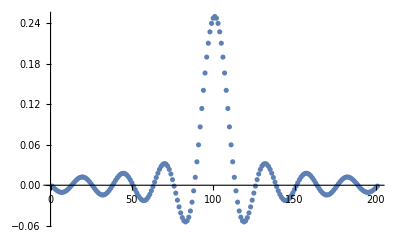

```mathematica
sinc=N@cutoff/Pi*Sinc[cutoff*Range[-100,100]/Pi];
ListPlot[sinc,PlotRange->Full]
```

Convolve the input signal with the generated sinc function

```mathematica
lowpass=ListConvolve[sinc,handel];
```

```mathematica
playSound[lowpass,fs]
```

```mathematica
plotFFT[lowpass]
```

-Graphics-

```mathematica
cutoff=Pi/8;
sinc=N@cutoff/Pi*Sinc[cutoff*Range[-100,100]/Pi];
```

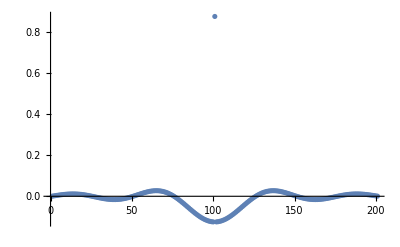

```mathematica
highpassKernel = Join[ConstantArray[0,100],{1},ConstantArray[0,100]]-sinc;
ListPlot[highpassKernel,PlotRange->Full]
```

```mathematica
highpass=ListConvolve[highpassKernel,handel];
```

```mathematica
playSound[highpass,fs]
```

```mathematica
plotFFT@highpass
```

-Graphics-

```mathematica
With[{context="p5`"},If[Context[]==context,End[],"Not in context"]]
```

p5`

## 6. Radio decode

```mathematica
With[{context="p6`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
lowpass[signal_,freq_]:=
Module[{sinc},
sinc=N@freq/Pi*Sinc[freq*Range[-60,60]/Pi];
(*ListPlot[sinc,PlotRange->Full];*)
ListConvolve[sinc,signal]
]
```

```mathematica
fs=Import["provided files/TwoAM.wav","SampleRate"]
encodedSignals=Import["provided files/TwoAM.wav","Data"];
```

44100

```mathematica
plotFFT@encodedSignals
```

-Graphics-

```mathematica
recoverSignal[data_,freq_]:=
Module[{shifted,filtered},
shifted= data*Cos[Pi freq*Range@Length@data];
filtered=lowpass[shifted,0.3 Pi];
filtered
]
```

Recover x[n]

```mathematica
freq=16000/fs;
x=recoverSignal[encodedSignals,freq];
```

```mathematica
playSound[x,fs];
```

```mathematica
plotFFT@x
```

-Graphics-

Recover w[n]

```mathematica
freq=6000/fs;
w=recoverSignal[encodedSignals,freq];
```

```mathematica
playSound[w,fs]
```

```mathematica
plotFFT@w
```

-Graphics-

```mathematica
With[{context="p6`"},If[Context[]==context,End[],"Not in context"]]
```

p6`

## Scratch work

```mathematica
exportNotebookPDF[]
```

/home/eric/Documents/School/QEA2/Acoustic Modem/Bset 3/Mathematica scratch.pdf

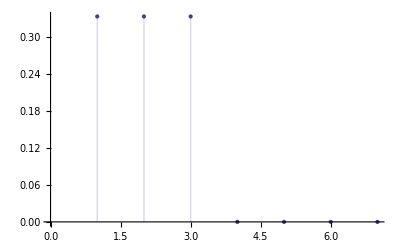

```mathematica
DiscretePlot[1/3 {1,1,1,0,0,0,0}⟦i⟧,{i,7},PlotTheme->"Classic",PlotRange->{{0,Automatic},Automatic}]
```

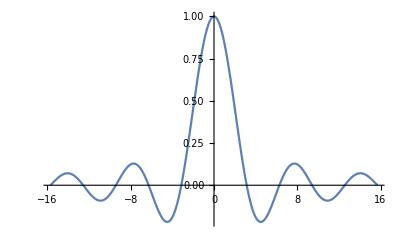

```mathematica
Plot[Sinc@x,{x,-5Pi,5Pi},PlotRange->All]
```